# 1D Graph states generation on Rydberg neutral atoms

Source of the experiment : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["../../quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../../../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

```mathematica
Options[RydbergHub]={
QubitNum-> 12,
AtomLocations->Association@Table[j->{j,0},{j,0,11}],
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.02, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.006,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.965,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.006,11->0.001|>
};
```

## Preparation

### Plots on the paper

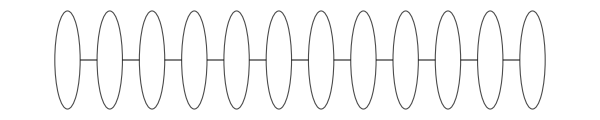

~/vqd/img/graph1d.pdf

```mathematica
g=Graph[#<->#+1&/@Range[0,10]];
Graph[g,VertexSize->0.6,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{13,FontFamily->"Serif"},ImageSize->600,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center]]
Export["~/vqd/img/graph1d.pdf",%]
```

```mathematica
showgs[title_:"",opt_:{}]:=PlotAtoms[devGS,Sequence@@opt,ImageSize->900,ShowBlockade->Range[0,11],LabelStyle->Directive[17,Black],BaseStyle->{16,FontFamily->"Times"},PlotRange->{{-1,37},{-1.3,1.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.96,0.15}]],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],
FrameTicks->{{{-1,0,1},None},{Automatic,None}}
];
```

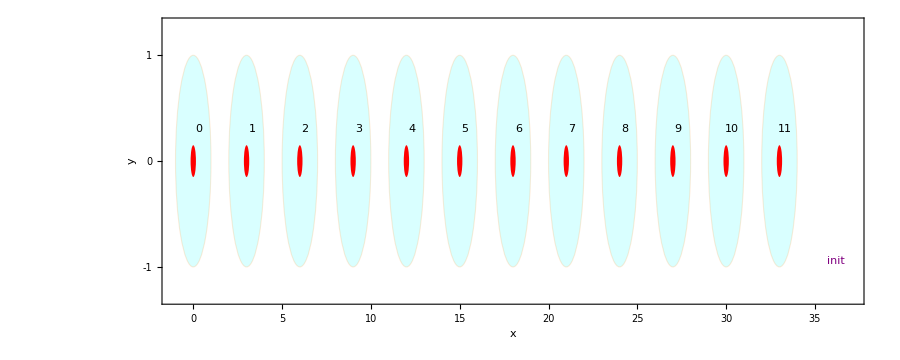

```mathematica
devGS=RydbergHub[];
showgs["init"]
```

```mathematica
circ1=CircRydbergHub[Flatten@{{Subscript[Init, #],Subscript[Ry, #][π/2]}&/@Range[0,11]},RydbergHub[],Parallel->True];
circ2={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{-0.75,0}]}};
circ3={Subscript[C, #][Subscript[Z, #+1]]&/@Range[0,10,2]};
circ4={{Subscript[ShiftLoc, Sequence@@Range[1,11,2]][{1.5,0}]}};
circ5={Subscript[C, #][Subscript[Z, #+1]]&/@Range[1,9,2]};
```

```mathematica
devGS=RydbergHub[];
f1=showgs["initial",{ImagePadding->{{30,20},{0,0}}}];
noisycirc1=InsertCircuitNoise[circ1,devGS];
noisycirc2=InsertCircuitNoise[circ2,devGS];
f2=showgs["move 1",{ImagePadding->{{30,20},{0,0}}}];
noisycirc3=InsertCircuitNoise[circ3,devGS];
noisycirc4=InsertCircuitNoise[circ4,devGS];
f3=showgs["move 2",{ImagePadding->{{30,20},{20,0}}}];
noisycirc5=InsertCircuitNoise[circ5,devGS];
```

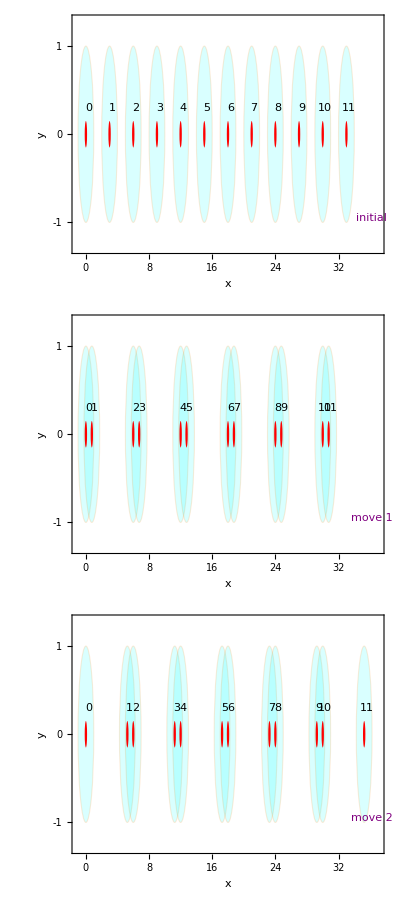

~/vqd/img/rydberg_graph.pdf

```mathematica
Column[{f1,f2,f3},Spacings->0]
Export["~/vqd/img/rydberg_graph.pdf",%]
```

#### Initialisation test

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[12];
ρinit=CreateDensityQureg[12];
ρwork=CreateDensityQureg[12];
```

```mathematica
(*returns graph state stabilizer of a node*)
stabgs[graph_,node_]:=With[{neig=Complement[VertexList@NeighborhoodGraph[graph,node],{node}]},
ToExpression[StringRiffle[Join[{Subscript[X, node]},Subscript[Z, #]&/@neig]]]]
```

Total  circuit excluding measurement

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
totalcirc=Join@@(ToExpression["circ"<>ToString@#]&/@Range[1,5])
```

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8,Init_9,Init_10,Init_11},{Ry_0[π/2],Ry_1[π/2],Ry_2[π/2],Ry_3[π/2],Ry_4[π/2],Ry_5[π/2],Ry_6[π/2],Ry_7[π/2],Ry_8[π/2],Ry_9[π/2],Ry_10[π/2],Ry_11[π/2]},{ShiftLoc_(1,3,5,7,9,11)[{-0.75,0}]},{C_0[Z_1],C_2[Z_3],C_4[Z_5],C_6[Z_7],C_8[Z_9],C_10[Z_11]},{ShiftLoc_(1,3,5,7,9,11)[{1.5,0}]},{C_1[Z_2],C_3[Z_4],C_5[Z_6],C_7[Z_8],C_9[Z_10]}}

```mathematica
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[]];
(*Simplify, remove errors with zero-parameters *)
enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
```

Run the circuit without measurement. We start from an unknown mixed state

```mathematica
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc]
```

{}

Benchmarking the perfect measurement. Quoted value: 0.91. Noisy: 0.87

{0.915149,0.914063,0.915164,0.914066,0.915164,0.914066,0.915164,0.914066,0.915164,0.914066,0.915161,0.914051}

0.914612

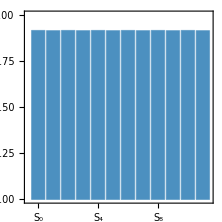

```mathematica
stabdata=CalcExpecPauliString[ρ,stabgs[g,#],ρwork]&/@Range[0,11]
Mean@stabdata
BarChart[stabdata,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}]
```

Gather the statistics by shots

Note that the “X” measurement done in the circuit is flipped: H=Ry[π/2]X

```mathematica
CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[X, 0]}]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
DrawCircuit@{Subscript[Ry, 0][π/2],Subscript[X, 0]}
```

-Graphics-

```mathematica
CalcCircuitMatrix[Subscript[X, 0]].CalcCircuitMatrix[Subscript[Ry, 0][π/2]]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
(*Two measurement settings: {Subscript[S, j]} where (1) j are even, (2) j are odd  
Put measurements at the very last!*)
evensm={Subscript[Ry, #][π/2]&/@Range[0,11,2],Subscript[M, #]&/@Range[0,11]};
oddsm={Subscript[Ry, #][π/2]&/@Range[1,11,2],Subscript[M, #]&/@Range[0,11]};
```

```mathematica
SimulateGraphState[ρ_,ρinit_,ρwork_,ρstore_,nshots_,options_:{}]:=Module[{noisycirc,enoisycirc,emeasnoisy,omeasnoisy,statevenmeas={},statoddmeas={},scount,outeig,stabideal,totalcirc},
totalcirc={{Subscript[Init, 0],Subscript[Init, 1],Subscript[Init, 2],Subscript[Init, 3],Subscript[Init, 4],Subscript[Init, 5],Subscript[Init, 6],Subscript[Init, 7],Subscript[Init, 8],Subscript[Init, 9],Subscript[Init, 10],Subscript[Init, 11]},{Subscript[Ry, 0][π/2],Subscript[Ry, 1][π/2],Subscript[Ry, 2][π/2],Subscript[Ry, 3][π/2],Subscript[Ry, 4][π/2],Subscript[Ry, 5][π/2],Subscript[Ry, 6][π/2],Subscript[Ry, 7][π/2],Subscript[Ry, 8][π/2],Subscript[Ry, 9][π/2],Subscript[Ry, 10][π/2],Subscript[Ry, 11][π/2]},{Subscript[ShiftLoc, 1,3,5,7,9,11][{-0.75,0}]},{Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 2][Subscript[Z, 3]],Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 6][Subscript[Z, 7]],Subscript[C, 8][Subscript[Z, 9]],Subscript[C, 10][Subscript[Z, 11]]},{Subscript[ShiftLoc, 1,3,5,7,9,11][{1.5,0}]},{Subscript[C, 1][Subscript[Z, 2]],Subscript[C, 3][Subscript[Z, 4]],Subscript[C, 5][Subscript[Z, 6]],Subscript[C, 7][Subscript[Z, 8]],Subscript[C, 9][Subscript[Z, 10]]}};
noisycirc=InsertCircuitNoise[totalcirc,RydbergHub[Sequence@@options]];
(*Simplify, remove errors with zero-parameters *)
     enoisycirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.]}];
ApplyCircuit[CloneQureg[ρ,ρinit],enoisycirc];
CloneQureg[ρstore,ρ];
emeasnoisy=ExtractCircuit@InsertCircuitNoise[evensm,RydbergHub[Sequence@@options]];
omeasnoisy=ExtractCircuit@InsertCircuitNoise[oddsm,RydbergHub[Sequence@@options]];

Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* even measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statevenmeas,Flatten@ApplyCircuit[ρ,emeasnoisy]];
(* odd measurements*)
CloneQureg[ρ,ρstore];
AppendTo[statoddmeas,Flatten@ApplyCircuit[ρ,omeasnoisy]];
,{nshots}];
(* stabilizer count *)
scount=Association@Table[j->0,{j,VertexList@g}];
(* First measurement setting: X,Z,X,Z...*)
Table[
outeig=Table[
If[EvenQ[k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
(* +1 - -1 *)
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,0,11,2}];
,{out,statevenmeas}];

(* Second measurement setting: Z,X,Z,X...*)
Table[
outeig=Table[
If[OddQ[k-1],
out[[k]]/.{0:>-1}, (*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];
Table[
scount[node]+=Times@@(outeig[[#+1]]&/@VertexList[NeighborhoodGraph[g,node]]);
,{node,1,11,2}];
,{out,statoddmeas}];
stabideal=CalcExpecPauliString[CloneQureg[ρ,ρstore],stabgs[g,#],ρwork]&/@Range[0,11];
Print[options];
Print[Show[
BarChart[Values@scount/nshots,ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,11]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->1,ChartStyle->ColorData["Rainbow"][0.3],PlotRange->{Automatic,{0,1}}],
ListPlot[{stabideal,stabideal},Joined->{False,True},PlotStyle->{Red,Black}],ImageSize->200
]," noisy<Sj>=",N@Mean@Values[scount/nshots],"  ideal<Sj>=",Mean[stabideal]];
<|"opt"->options,"outeven"->statevenmeas,"outodd"->statoddmeas,"scount"->scount,"sideal"->stabideal|>
]
```

## Simulating the stabiliser measurement

```mathematica
DestroyAllQuregs[];
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[12,4];
```

```mathematica
SetQuregMatrix[ρinit,RandomMixState[12]];
```

```mathematica
outputsgs=SimulateGraphState[ρ,ρinit,ρwork,ρstore,500,{}]
```

OptionValue::optnf: Option name DurMove not found in defaults for RydbergHub.

OptionValue::optnf: Option name HeatFactor not found in defaults for RydbergHub.

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

OptionValue::optnf: Option name DurMove not found in defaults for RydbergHub.

General::stop: Further output of OptionValue::optnf will be suppressed during this calculation.

```mathematica
(* try some combinations of error parameters *)
fbrot=Flatten@Table[<|10->i,01->j|>,{i,{0.01,0.02}},{j,{0.02,0.03}}];
probleakinit={0.001,0.01};
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.01,0.05}},{j,{0.005,0.001}}];
fidmeas={0.97,0.98,0.98,0.99};
options=Flatten[Table[{ProbBFRot->i,ProbLeakInit->j,ProbLeakCZ->k,FidMeas->l},{i,fbrot},{j,probleakinit},{k,probleakcz},{l,fidmeas}],3];
```

```mathematica
(* run the simulation *)
(*outputsgs=SimulateGraphState[ρ,ρinit,ρwork,ρstore,2000,#]&/@options;*)
```